{schoolboard,adriennearscht,museumpark,eleventhstreet,parkwest,freedomtower,collegenortho,wilkiedfergusono,governmentcentero,thirdstreeto,knightcentero,knightcenteri}

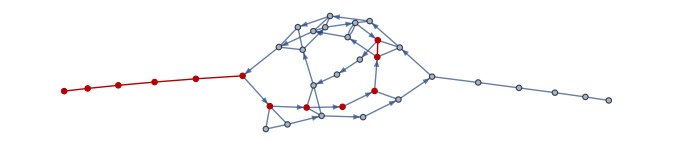

```mathematica
g =Import[SystemDialogInput["FileOpen"]];
graphData = Graph[g];
stationList= DeleteDuplicates[StringSplit[StringReplace[ToString[g],{WhitespaceCharacter :>"","\"":>"","{" :>"","}":>""}],{",","<->","->","{","}"}]];
dropdown = PopupMenu[Dynamic[y],stationList]
dropdownTwo = PopupMenu[Dynamic[tru],stationList]
results = FindShortestPath[graphData,ToExpression[y], ToExpression[tru], Method->"Dijkstra"];
Print[results];
HighlightGraph[graphData,PathGraph[results]]
```